# Mathematica Basics

## Basics

Mathematica is a rich-text mathematics editor - much like Jupyter Notebooks or .mlx files in MATLAB. .nb files can be formatted just like Word documents, where you can mix in equations, executable code, and pictures. 
The number one thing to remember in Mathematica is all built-in functions are Capitalized and take arguments between square brackets [ ]

## A notebook is made from “cells”

Everything in Mathematica from text to input is contained within cells.

Any formatting will apply to the entire cell

Press Shift+Enter to evaluate cell

Press Ctrl+Shift+d to divide cell

Press Alt+Enter to start new cell of the same type

```mathematica
X=8
```

8

```mathematica
(3* y +9)^3//Expand
```

729+729 y+243 y^2+27 y^3

## Lists

Mathematica is build on lists. They are the most general structure in Mathematica. You can build them in several ways:

```mathematica
flist = {3,4,5,6,7,8}
slist = List[3,4,5,6,7,8]
rlist = Range[3,8]
rlist2 = Range[3,8,1/4]//N
mixlist = {2,"catch",4,5,True}
```

{3,4,5,6,7,8}

{3,4,5,6,7,8}

{3,4,5,6,7,8}

{3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.,5.25,5.5,5.75,6.,6.25,6.5,6.75,7.,7.25,7.5,7.75,8.}

{2,catch,4,5,True}

You can use indexing to extract elements just as in MATLAB or Python, with slightly different syntax:

```mathematica
flist[[4]]
flist[[2;;5]]
3*flist[[3;;]]
3*mixlist[[2]]
```

6

{4,5,6,7}

{15,18,21,24}

3 catch

You can apply functions directly to list - the functions will return lists :

```mathematica
Sqrt[flist]
Sqrt[flist]//N
Log[mixlist]//N
```

{√3,2,√5,√6,√7,2 √2}

{1.73205,2.,2.23607,2.44949,2.64575,2.82843}

{0.693147,Log[catch],1.38629,1.60944,Log[True]}

There is a plethora of useful functions you can use to manipulate lists:

```mathematica
v=RandomInteger[{1,50},10]
```

{6,47,10,16,1,18,2,5,28,18}

```mathematica
Sort[v]
Union[v]
Reverse[v]
Prepend[v,4.5]
Append[v,4.5]
newv = Delete[v,6]
```

{1,2,5,6,10,16,18,18,28,47}

{1,2,5,6,10,16,18,28,47}

{18,28,5,2,18,1,16,10,47,6}

{4.5,6,47,10,16,1,18,2,5,28,18}

{6,47,10,16,1,18,2,5,28,18,4.5}

{6,47,10,16,1,2,5,28,18}

## Import Data

Mathematica can import numerous file formats, including ones produced by other programs. (When importing files, be extra careful with your directory path).

```mathematica
sun = Import["C:\\Users\\tomke\\My Drive\\Programs\\courses\\main\\Mathematica\\sunspotsbyyear.csv"];
```

It will most likely be imported as a nested list - a list of lists. Use the same syntax to extract elements

{8.3,18.3,26.7,38.3,60,96.7,48.3,33.3,16.7,13.3,5,0,0,3.3,18.3,45,78.3,105,100,65,46.7,43.3,36.7,18.3,35,66.7,130,203.3,171.7,121.7,78.3,58.3,18.3,8.3,26.7,56.7,116.7,135,185,168.3,121.7,66.7,33.3,26.7,8.3,18.3,36.7,66.7,100,134.8,139,79.5,79.7,51.2,20.3,16,17,54,79.3,90,104.8,143.2,102,75.2,60.7,34.8,19,63,116.3,176.8,168,136,110.8,58,51,11.7,33,154.2,257.3,209.8,141.3,113.5,64.2,38,17,40.2,138.2,220,218.2,196.8,149.8,111,100,78.2,68.3,35.5,26.7,10.7,6.8,11.3,24.2,56.7,75,71.8,79.2,70.3,46.8,16.8,13.5,4.2,0,2.3,8.3,20.3,23.2,59,76.3,68.3,52.9,38.5,24.2,9.2,6.3,2.2,11.4,28.2,59.9,83,108.5,115.2,117.4,80.8,44.3,13.4,19.5,85.8,192.7,227.3,168.7,143,105.5,63.3,40.3,18.1,25.1,65.8,102.7,166.3,208.3,182.5,126.3,122,102.7,74.1,39,12.7,8.2,43.4,104.4,178.3,182.2,146.6,112.1,83.5,89.2,57.8,30.7,13.9,62.8,123.6,232,185.3,169.2,110.1,74.5,28.3,18.9,20.7,5.7,10,53.7,90.5,99,106.1,105.8,86.3,42.4,21.8,11.2,10.4,11.8,59.5,121.7,142,130,106.6,69.4,43.8,44.4,20.2,15.7,4.6,8.5,40.8,70.1,105.5,90.1,102.8,80.9,73.2,30.9,9.5,6,2.4,16.1,79,95,173.6,134.6,105.7,62.7,43.5,23.7,9.7,27.9,74,106.5,114.7,129.7,108.2,59.4,35.1,18.6,9.2,14.6,60.2,132.8,190.6,182.6,148,113,79.2,50.8,27.1,16.1,55.3,154.3,214.7,193,190.7,118.9,98.3,45,20.1,6.6,54.2,200.7,269.3,261.7,225.1,159,76.4,53.4,39.9,15,22,66.8,132.9,150,149.4,148,94.4,97.6,54.1,49.2,22.5,18.4,39.3,131,220.1,218.9,198.9,162.4,91,60.5,20.6,14.8,33.9,123,211.1,191.8,203.3,133,76.1,44.9,25.1,11.6,28.9,88.3,136.3,173.9,170.4,163.6,99.3,65.3,45.8,24.7,12.6,4.2,4.8,24.9,80.8,84.5,94,113.3,69.8}

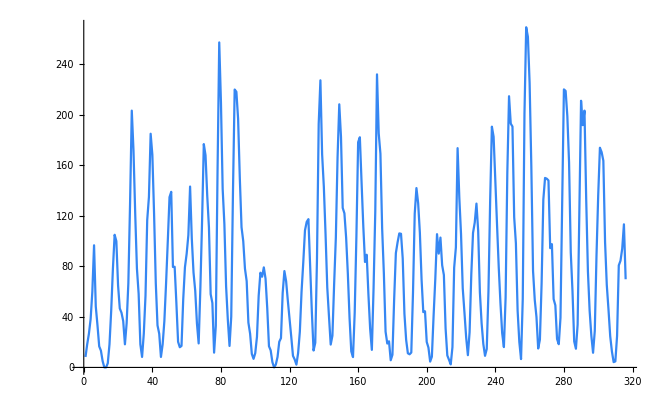

```mathematica
sun;
sun=Flatten[sun];
sun = Partition[sun,5];
sun[[9]];
sun[[9,2]];
sun[[All,2]]
ListPlot[sun[[All,2]],Joined->True]
```

## Defining Functions

There are 3 common ways to define functions in Mathematica

```mathematica
f = Function[{x,y},x^2+y^2];
g = (#1^2+#2^2) &;
h[x_,y_] := x^2+y^2;
f[2,3]
g[2,3]
h[2,3]
```

13

13

13

I do prefer the explicitly definition

h[x_,y_] := x^2+y^2

The := is a delayed assignment operator, meaning that every time you call h, Mathematica will return and redefine the function. This is a very nice option since parameters inside your function definition could change from when it is created to when it is called. For example, try the code below by assigning fun with = and then with :=

```mathematica
a=2;
F[x_]:= (a*x^3)/(Exp[x]-1);
G[x_] = (a*x^3)/(Exp[x]-1);
```

```mathematica
F[2]-G[2]
a=5;
F[2]-G[2]
```

16/(-1+ⅇ^2)

24/(-1+ⅇ^2)

```mathematica
G[x]
```

(2 x^3)/(-1+ⅇ^x)

```mathematica
F[x]
```

(5 x^3)/(-1+ⅇ^x)

```mathematica
xRange[v_,θ_,h_,g_] := (v^2 Cos[θ] Sin[θ])/g+√((v^4 Cos[θ]^2 Sin[θ]^2)/g^2+(2 h v^2 Cos[θ]^2)/g);
xRange[45,60*π/180,0,9.81]
Sqrt[4]+ 6^2
Cos[π]//N
```

178.767

38

-1.

## More Advanced Mathematical Operations

Mathematica’s great advantage over other programming languages is it’s symbolic engine. Mathematica can perform symbolic calculations on almost any analytic expression. Not only that but it can then numerically evaluate those same expressions. Let’s look at some examples:

#### Simple Equation Solving

```mathematica
xsol=Solve[x^3-x-9==0,x]//N
```

{{x→2.24004},{x→-1.12002-1.66233 ⅈ},{x→-1.12002+1.66233 ⅈ}}

```mathematica
xsol=Flatten[xsol]
6*x^2-8*x/.xsol[[1]]//N
```

{x→2.24004,x→-1.12002-1.66233 ⅈ,x→-1.12002+1.66233 ⅈ}

12.1864

#### System of Equations

The classic physics example of a situation requiring a system of equations is simple DC circuits (although, more complex circuits require them too). Let’s look at a circuit like this one:
-Graphics-

Recalling Kirchhoff’s Laws, the system of equations that relate all the currents, voltages, and resistors for this circuit is

V_1 -i_1 R_1-i_2 R_2+V_2-i_1 R_1 = 0
V_2 +i_3 R_1+i_3 R_2+V_3-i_2 R_2 = 0
i_1=i_2+i_3

Coding this into Mathematica,

```mathematica
currents=Solve[{Subscript[V, 1] -Subscript[i, 1] Subscript[R, 1]-Subscript[i, 2] Subscript[R, 2]+Subscript[V, 2]-Subscript[i, 1] Subscript[R, 1] == 0,Subscript[V, 2] +Subscript[i, 3] Subscript[R, 1]+Subscript[i, 3] Subscript[R, 2]+Subscript[V, 3]-Subscript[i, 2] Subscript[R, 2] == 0,Subscript[i, 1]==Subscript[i, 2]+Subscript[i, 3]},{Subscript[i, 1],Subscript[i, 2],Subscript[i, 3]}]
```

{{i_1→-(-R_1 V_1-2 R_2 V_1-R_1 V_2-R_2 V_2+R_2 V_3)/(2 R_1^2+5 R_1 R_2+R_2^2),i_2→-(-R_1 V_1-R_2 V_1-3 R_1 V_2-R_2 V_2-2 R_1 V_3)/(2 R_1^2+5 R_1 R_2+R_2^2),i_3→-(-R_2 V_1+2 R_1 V_2+2 R_1 V_3+R_2 V_3)/(2 R_1^2+5 R_1 R_2+R_2^2)}}

```mathematica
currents2=Flatten[currents]
```

{i_1→-(-R_1 V_1-2 R_2 V_1-R_1 V_2-R_2 V_2+R_2 V_3)/(2 R_1^2+5 R_1 R_2+R_2^2),i_2→-(-R_1 V_1-R_2 V_1-3 R_1 V_2-R_2 V_2-2 R_1 V_3)/(2 R_1^2+5 R_1 R_2+R_2^2),i_3→-(-R_2 V_1+2 R_1 V_2+2 R_1 V_3+R_2 V_3)/(2 R_1^2+5 R_1 R_2+R_2^2)}

```mathematica
I1[Subscript[V, 1]_]=currents2[[1,2]]
```

-(-R_1 V_1-2 R_2 V_1-R_1 V_2-R_2 V_2+R_2 V_3)/(2 R_1^2+5 R_1 R_2+R_2^2)

```mathematica
Subscript[i, 1]-Subscript[i, 2]-Subscript[i, 3]/.currents2 
Subscript[i, 1]-Subscript[i, 2]-Subscript[i, 3]/.currents2//FullSimplify
```

(-R_1 V_1-R_2 V_1-3 R_1 V_2-R_2 V_2-2 R_1 V_3)/(2 R_1^2+5 R_1 R_2+R_2^2)-(-R_1 V_1-2 R_2 V_1-R_1 V_2-R_2 V_2+R_2 V_3)/(2 R_1^2+5 R_1 R_2+R_2^2)+(-R_2 V_1+2 R_1 V_2+2 R_1 V_3+R_2 V_3)/(2 R_1^2+5 R_1 R_2+R_2^2)

0

#### Hydrogen Atom Wavefunction

The wavefunctions for the hydrogen atom are combinations of Laguerre Polynomials and Spherical Harmonic functions, both of which are built-in functions of Mathematica. Here is the wave function for the n=3, l=0, m_l=0 wavefunction:

```mathematica
ψ[r_,ϕ_,θ_] := 1/(81 √(3*π*a^3))(27-18*r/a+2*r^2/a^2)Exp[-r/(3*a)]
ω α Ψ 
D[ψ[r,ϕ,θ],r]//FullSimplify
ψ[2,π/2,π]//N
```

```mathematica
Integrate[Integrate[Integrate[ψ[r,ϕ,θ]^2*r^2*Sin[θ],{r,0,a}],{ϕ,0,2*π}],{θ,0,π}]//N
```

You’ll look at the Spherical Harmonic functions in Mathematica_Lesson.nb.

#### Pendulum, small-angle approximation

```mathematica
Clear[g,L]
sol = DSolve[{θ''[t] == -g/L*θ[t],θ[0]==0.03,θ'[0]==0},θ[t],t]
```

{{θ[t]→0.03 Cos[(√g t)/(√L)]}}

```mathematica
sol[[1,1,2]]
```

0.03 Cos[(√g t)/(√L)]

Non-linear Pendulum Problem

```mathematica
g = 9.8;
L = 1;
sol = NDSolve[{θ''[t] == -g/L*Sin[θ[t]],θ[0]==π/2,θ'[0]==0},θ[t],{t,0,20}]
```

{{θ[t]→InterpolatingFunction[…][t]}}

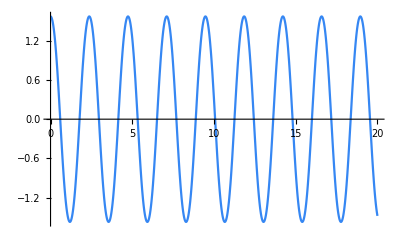

```mathematica
Plot[θ[t]/.sol,{t,0,20}]
```

```mathematica
T[theta0_] := NIntegrate[4*√(L/(2g))1/(√(Cos[θ]-Cos[theta0])),{θ,0,theta0}]
```

```mathematica
T[π]
```

48.5866

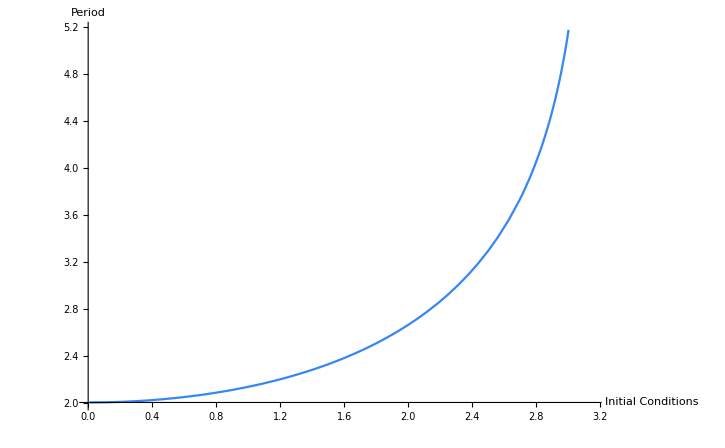

```mathematica
Plot[T[x],{x,0.01,π},AxesLabel->{"Initial Conditions","Period"}]
```

```mathematica
sun1
```